## Mirror Geometry

References: 
- Tao, X. (2014), A numerical study of chorus generation and the related variation of wave intensity using the DAWN code, 
J. Geophys. Res. Space Physics, 119, 3362-3372, doi:10.1002/2014JA019820.
- Ke, Y., Gao, X., Lu, Q., Wang, X., and Wang, S. (2017), Generation of rising-tone chorus in a two-dimensional mirror field by using the general curvilinear PIC code, 
J. Geophys. Res. Space Physics, 122, 8154-8165, doi:10.1002/2017JA024178.

### Mirror Magnetic Field

We choose a Cartesian coordinate system where the origin coincides with the center of mirror geometry.
We choose the x coordinate along the mirror magnetic field at the center of mirror geometry.
Then, the x component of the background magnetic field may be written as
B_x(𝕣)=B_x(x)=B_0(1+ξ^2 x^2),
where B_0 is the mirror magnetic field at the origin and ξ is the inhomogeneity parameter and in units of inverse of length.
Consider cylindrical coordinates, (x,s,ϕ), where
x=x; 
y=s cosϕ; 
z=s sinϕ.
The unit vectors are given by
𝕖_x=𝕖_x; 
𝕖_s=cosϕ 𝕖_y+sinϕ 𝕖_z; 
𝕖_ϕ=-sinϕ 𝕖_y+cosϕ 𝕖_z.
Making use of cylindrical symmetry, the divergence-free condition of the magnetic field yields
0=∇·𝔹=(∂B_x)/(∂x)+1/s∂/(∂s)(s B_s)+1/s(∂B_ϕ)/(∂ϕ) → ∂/(∂s)(s B_s)=-s(∂B_x)/(∂x).
Integrating both sides with B_s(s=0)=0 as the boundary condition yields
(s B_s)=-(B_0 2 ξ^2 x)s^2/2
B_s=-B_0 ξ^2 x s.
We also have B_ϕ=0.
Therefore, the mirror magnetic field vector is given by 
𝔹=B_x 𝕖_x+B_s 𝕖_s
=B_x 𝕖_x+B_s cosϕ 𝕖_y+B_s sinϕ 𝕖_z.
Substituting B_s, we can get the expressions for B_y and B_z. 
Hence all three Cartesian components read
(B_x
B_y
B_z)=B_0(1+ξ^2 x^2
-ξ^2x y
-ξ^2x z).
The magnitude of the field is
B^2=B_x^2+B_s^2=B_0^2((1+ξ^2 x^2)^2+ξ^4 x^2 s^2)
=B_x^2(1+(ξ^4 x^2 s^2)/((1+ξ^2 x^2)^2)).
From the condition d𝕣=dx 𝕖_x+ds 𝕖_s+s dϕ 𝕖_ϕ=k 𝔹 (k is a constant scale factor), the field line equation is given by
ϕ=const; 
dx/B_x=ds/B_s
dx/(1+ξ^2 x^2)=ds/(-ξ^2x s)
ds/s=(-ξ^2x)/(1+ξ^2 x^2)dx
Log[s]=-1/2Log[1+ξ^2 x^2]+k
s=s_0/(√(1+ξ^2 x^2))=s_0/(√(B_x(x)/B_0)),
where s_0 is an integral constant and chosen such that s(x=0)=s_0.
The Cartesian coordinates of the field line position vector are
(x
y
z)=(x
y_0/(√(1+ξ^2 x^2))
z_0/(√(1+ξ^2 x^2))).
The field line arc length (for a given s_0) is given by
d r^2=d x^2+d s^2=d x^2+(ξ^4 x^2 s_0^2)/((1+ξ^2 x^2)^3)d x^2
=(1+(ξ^4 x^2 s_0^2)/((1+ξ^2 x^2)^3))d x^2
=(1+(ξ^4 x^2 s^2)/((1+ξ^2 x^2)^2))d x^2
=B^2/B_x^2 d x^2.

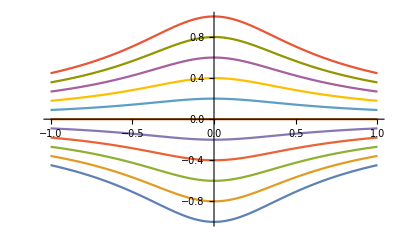

```mathematica
With[{ξ=2,z0=0,y0=Range[-1,1,.2],xlim={-1,1}},
Module[{xs,ys},
xs=Array[N,101,xlim];
ys=Divide[#,Sqrt[1+ξ^2xs^2]]&/@y0;
ListPlot[ys,DataRange->xlim,Joined->True]
]
]
```

### Curvilinear Coordinates

Let us define field line-agnostic curvilinear coordinates, (q^1,q^2,q^3).
We choose the field-aligned coordinate, q^1, such that a unit length in q^1 corresponds to a field line arc length
proportional to the mirror magnetic field. Formally,
Δ_1 ⅆ q^1=ⅆr/(B/B_0)=(B/B_x)/(B/B_0)ⅆx=B_0/B_x ⅆx=1/(1+ξ^2 x^2)ⅆx,
where Δ_1 is the scaling factor (constant) between ⅆ q^1 and ⅆx.
Integrating both sides with the boundary condition q^1(x=0)=0 yields
Δ_1 q^1=1/ξ tan^-1 ξ x.
Because the cross sectional area of the flux tube at a given location x is proportional to sⅆs or B_x^-1,
if we choose q^2 (q^3) proportional to y_0 (z_0), the volume element represented by Δ q^1 Δ q^2 Δ q^3 will remain constant.
So, similarly
Δ_2 q^2=y_0=√(1+ξ^2 x^2)y;
Δ_3 q^3=y_0=√(1+ξ^2 x^2)z.
In summary, the field-aligned curvilinear coordinates are
(Δ_1 q^1
Δ_2 q^2
Δ_3 q^3)=(1/ξ tan^-1 ξ x
√(1+ξ^2 x^2)y
√(1+ξ^2 x^2)z).
To express the Cartesian coordinates in terms of the curvilinear coordinates, notice 
x=1/ξ tan(ξ Δ_1 q^1) or ξ^2 x^2=tan^2(ξ Δ_1 q^1).
Making use of 1/(√(1+tan^2 θ))=cosθ for -π/2<θ<π/2, the Cartesian coordinates read
(x
y
z)=(1/ξ tan(ξ Δ_1 q^1)
Δ_2 q^2 cos(ξ Δ_1 q^1)
Δ_3 q^3 cos(ξ Δ_1 q^1)).
For the limiting case ξ→0, we have
(x
y
z)=(Δ_1 q^1
Δ_2 q^2
Δ_3 q^3), 
in which the meaning of the grid scaling factor Δ_j becomes clear.

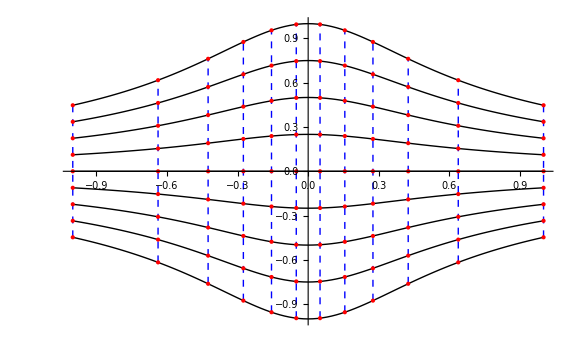

```mathematica
With[{ξ=2,z0=0,y0lim={-1,1},xlim={-1,1},nq1=12,nq2=9},
Module[{xs,ys,Δ1q1s,Δ2q2s,grid},
xs=Array[N,101,xlim];
ys=Divide[#,Sqrt[1+ξ^2xs^2]]&/@Array[N,nq2,y0lim];
Δ1q1s=Array[N,nq1,ArcTan[ξ xlim]/ξ];
Δ2q2s=Array[N,nq2,y0lim];
grid=Function[{Δ1q1,Δ2q2},{Tan[ξ Δ1q1]/ξ,Δ2q2 Cos[ξ Δ1q1]},{Listable}];
grid=grid[#,Δ2q2s]&/@Δ1q1s;
Show[
ListPlot[ys,DataRange->xlim,Joined->True,PlotStyle->Directive[Thickness[Small],Black]],
Graphics[{
{Blue,Dashed,Line/@grid},
{Red,PointSize[Medium],Point[Join@@grid]}
}],
ImageSize->Large
]
]
]
```

Having established the relationship between the two different coordinate sets, let us now find the metric and basis vectors.
The covariant basis vectors are given by 𝕘_j=(∂𝕣)/(∂q^j):
𝕘_1=(∂𝕣)/(∂q^1)=Δ_1 sec^2(ξ Δ_1 q^1)𝕖_x-Δ_1 ξ Δ_2 q^2 sin(ξ Δ_1 q^1)𝕖_y-Δ_1 ξ Δ_3 q^3 sin(ξ Δ_1 q^1)𝕖_z
=Δ_1(sec^2(ξ Δ_1 q^1)𝕖_x-ξ Δ_2 q^2 sin(ξ Δ_1 q^1)𝕖_y-ξ Δ_3 q^3 sin(ξ Δ_1 q^1)𝕖_z)
=Δ_1((1+ξ^2 x^2)𝕖_x-ξ^2 x y 𝕖_y-ξ^2 x z 𝕖_z)
=Δ_1 𝔹/B_0;
𝕘_2=(∂𝕣)/(∂q^2)=Δ_2 cos(ξ Δ_1 q^1)𝕖_y=Δ_2/(√(1+ξ^2 x^2))=Δ_2 √(B_0/B_x)𝕖_y;
𝕘_3=(∂𝕣)/(∂q^3)=Δ_3 cos(ξ Δ_1 q^1)𝕖_z=Δ_3/(√(1+ξ^2 x^2))=Δ_3 √(B_0/B_x)𝕖_z;
where we have used
sec^2(ξ Δ_1 q^1)=1+ξ^2 x^2=B_x/B_0;
sin^2(ξ Δ_1 q^1)=1-1/(sec^2(ξ Δ_1 q^1))=(ξ^2 x^2)/(1+ξ^2 x^2).
The covariant components of the metric tensor are
g_ij=𝕘_i·𝕘_j
=(Δ_1^2 B^2/B_0^2 | Δ_1 Δ_2 √(B_0/B_x)B_y/B_0 | Δ_1 Δ_3 √(B_0/B_x)B_z/B_0
Δ_1 Δ_2 √(B_0/B_x)B_y/B_0 | Δ_2^2 B_0/B_x | 0
Δ_1 Δ_3 √(B_0/B_x)B_z/B_0 | 0 | Δ_3^2 B_0/B_x)=(Δ_1^2((1+ξ^2 x^2)^2+ξ^4 x^2 s^2) | Δ_1 Δ_2(-ξ^2x y)/(√(1+ξ^2 x^2)) | Δ_1 Δ_3(-ξ^2x z)/(√(1+ξ^2 x^2))
Δ_1 Δ_2(-ξ^2x y)/(√(1+ξ^2 x^2)) | Δ_2^2 1/(1+ξ^2 x^2) | 0
Δ_1 Δ_3(-ξ^2x z)/(√(1+ξ^2 x^2)) | 0 | Δ_3^2 1/(1+ξ^2 x^2))
=(Δ_1^2(sec^4(ξ Δ_1 q^1)+((ξ Δ_2 q^2)^2+(ξ Δ_3 q^3)^2)sin^2(ξ Δ_1 q^1)) | Δ_1 Δ_2(-ξ Δ_2 q^2 sin(ξ Δ_1 q^1)cos(ξ Δ_1 q^1)) | Δ_1 Δ_3(-ξ Δ_3 q^3 sin(ξ Δ_1 q^1)cos(ξ Δ_1 q^1))
Δ_1 Δ_2(-ξ Δ_2 q^2 sin(ξ Δ_1 q^1)cos(ξ Δ_1 q^1)) | Δ_2^2 cos^2(ξ Δ_1 q^1) | 0
Δ_1 Δ_3(-ξ Δ_3 q^3 sin(ξ Δ_1 q^1)cos(ξ Δ_1 q^1)) | 0 | Δ_3^2 cos^2(ξ Δ_1 q^1)).
Note that
g=|g_ij|=Δ_1^2 Δ_2^2 Δ_3^2 
is independent of position.
Therefore, the differential volume element is
ⅆV=𝕘_1·(𝕘_2×𝕘_3)ⅆ q^1ⅆ q^2ⅆ q^3=Δ_1 Δ_2 Δ_3 ⅆ q^1ⅆ q^2ⅆ q^3=√g ⅆ q^1ⅆ q^2ⅆ q^3 
is also independent of position.

### Without inhomogeneity parameter

Cartesian components of the magnetic mirror field:
(B_x
B_y
B_z)=B_0(1+ξ^2 x^2
-2 ξ^2 x y
0),
where B_0 is the magnetic field at the origin and ξ is the inhomogeneity parameger (in unit of inverse length) and it satisfies ∇·𝔹=0.
Using dx/B_x=dy/B_y, the field line equation is
y=y_0/(1+ξ^2 x^2), where y_0 is the y coordinate at x=0 (i.e., field line label).

```mathematica
With[{ξ=1,y0=1.5,ny=9,Δ1=1,nq1=5},
Block[{x,q1,y0s,gridpts},
y0s=Range[ny,0,-1]y0/ny-y0/2;
q1=Divide[ArcTan[ξ y0],ξ Δ1]Range[-nq1,nq1]/nq1//N;
gridpts=Thread[{Tan[ξ Δ1 q1]/ξ,Divide[#,1+Tan[ξ Δ1 q1]^2]}]&/@y0s;
Show[
Plot[Divide[y0s,1+ξ^2x^2]//Evaluate,{x,-y0,y0},ImageSize->Large,ImagePadding->10,PlotStyle->Directive[Gray,Thickness[Medium]]],
Graphics[{
{Red,PointSize[Medium],Point/@gridpts},
{Gray,Thickness[Medium],Dashed,Line/@Transpose[gridpts]}
}]
]
]
]
```

We want the center grid spacing along the field line to be proportional to B[x,0], i.e., Δx∝B[x,0].
Integrating Δ_1 ⅆ q^1=ⅆx/(1+ξ^2 x^2), Δ_1 q^1=1/ξ tan^-1 ξ x+ℂ.
To make q^1[x=0]=0, we choose ℂ=0.
The horizontal grid spacing across the field line at the equator is constant.
Then the curvilinear coordinates are
(ξ Δ_1 q^1
ξ Δ_2 q^2)=(tan^-1 ξ x
(1+ξ^2 x^2)ξ y), where Δ_1 and Δ_2 are constant scale factors, and q^1 and q^2 are nondimensional.
Inverse of them are
(ξ x
ξ y)=(tan[ξ Δ_1 q^1]
(ξ Δ_2 q^2)/(1+tan^2[ξ Δ_1 q^1])).
The inhomogeneity factor may be absorbed into the length scale quantities (ξ x→x, ξ Δ_1→Δ_1, etc.). Then
(Δ_1 q^1
Δ_2 q^2)=(tan^-1 x
(1+x^2)y) ↔ (x
y)=(tan[Δ_1 q^1]
(Δ_2 q^2)/(1+tan^2[Δ_1 q^1]))

```mathematica
With[{assume=And[q1∈Reals,q2∈Reals,Δ1>0,Δ2>0,x∈Reals,y∈Reals]},
Module[{g1,g2,gij,g,h1,h2},
g1=D[{Tan[Δ1 q1],Divide[Δ2 q2,1+Tan[Δ1 q1]^2]},q1]/.{q1->ArcTan[x]/Δ1,q2->(1+x^2)y/Δ2};
g2=D[{Tan[Δ1 q1],Divide[Δ2 q2,1+Tan[Δ1 q1]^2]},q2]/.{q1->ArcTan[x]/Δ1,q2->(1+x^2)y/Δ2};
gij=FullSimplify[{{g1.g1,g1.g2},{g2.g1,g2.g2}},Assumptions->assume];
(*gij=FullSimplify[gij/.{x->Tan[Δ1 q1],y->Δ2 q2/(1+Tan[Δ1 q1]^2)},Assumptions->assume];*)
g=FullSimplify[Det[gij],Assumptions->assume];
h1=FullSimplify[Cross[Append[g2,0],{0,0,1}]/Sqrt[g]//Most,Assumptions->assume];
(*FullSimplify[h1/.{x->Tan[Δ1 q1],y->Δ2 q2/(1+Tan[Δ1 q1]^2)},Assumptions->assume]*)
h2=FullSimplify[Cross[{0,0,1},Append[g1,0]]/Sqrt[g]//Most,Assumptions->assume];
(*FullSimplify[h2/.{x->Tan[Δ1 q1],y->Δ2 q2/(1+Tan[Δ1 q1]^2)},Assumptions->assume]*)
]
]
```

Covariant bases:
𝕘_1=(∂𝕣)/(∂q^1)=Δ_1(sec^2[Δ_1 q^1]𝕖_x-Δ_2 q^2 sin[2 Δ_1 q^1]𝕖_y)=Δ_1((1+x^2)𝕖_x-2x y 𝕖_y)=Δ_1 𝔹/B_0
𝕘_2=(∂𝕣)/(∂q^2)=Δ_2 cos^2[Δ_1 q^1]𝕖_y=Δ_2/(1+x^2)𝕖_y
Covariant metric tensor:
g_ij=(Δ_1^2(1+x^4+2(1+2 y^2)x^2) | Δ_1 Δ_2(-2x y)/(1+x^2)
Δ_1 Δ_2(-2x y)/(1+x^2) | Δ_2^2/((1+x^2)^2))=(Δ_1^2(sec^4[Δ_1 q^1]+(Δ_2 q^2)^2 sin^2[2 Δ_1 q^1]) | Δ_1 Δ_2(-2 Δ_2 q^2 sin[Δ_1 q^1]cos^3[Δ_1 q^1])
Δ_1 Δ_2(-2 Δ_2 q^2 sin[Δ_1 q^1]cos^3[Δ_1 q^1]) | Δ_2^2 cos^4[Δ_1 q^1])
Determinant:
g=Det[g_ij]=(Δ_1 Δ_2)^2
Contravariant bases:
𝕘^1=(𝕘_2×𝕘_3)/(√g)=1/Δ_1 1/(1+x^2)𝕖_x=(cos^2[Δ_1 q^1])/Δ_1 𝕖_x
𝕘^2=(𝕘_3×𝕘_1)/(√g)=1/Δ_2(2x y 𝕖_x+(1+x^2)𝕖_y)=1/Δ_2(Δ_2 q^2 sin[2 Δ_1 q^1]𝕖_x+sec^2[Δ_1 q^1]𝕖_y)

Vector component transformation
𝕦=u^i 𝕘_i=u_i 𝕘^i=u_x 𝕖_x+u_y 𝕖_y
Contravariant to covariant components:
u_i=𝕦·𝕘_i=g_ij u^j
Contravariant to cartesian components:
(u_x
u_y)=(𝕦·𝕖_x
𝕦·𝕖_y)=(u^1 𝕘_1·𝕖_x+u^2 𝕘_2·𝕖_x
u^1 𝕘_1·𝕖_y+u^2 𝕘_2·𝕖_y)
Cartesian to contravariant components:
u^i=𝕦·𝕘^i=u_x 𝕖_x·𝕘^i+u_y 𝕖_y·𝕘^i

```mathematica
With[{Δ1=.1,Δ2=.06,nq1=6,nq2=10},
Module[{Δ1q1,Δ2q2,xy,g1,g2,h1,h2},
Δ1q1=Range[0,nq1]Δ1;
Δ2q2=Range[0,nq2]Δ2;
xy=Thread[{Tan[#],Δ2q2/(1+Tan[#]^2)}]&/@Δ1q1;
g1=Apply[Function[{x,y},Δ1{1+x^2,-2x y}],xy,{-2}].5;
g2=Apply[Function[{x,y},Δ2{0,1/(1+x^2)}],xy,{-2}].5;
h1=Apply[Function[{x,y},{1/(1+x^2),0}/Δ1],xy,{-2}].5Δ1 Δ2;
h2=Apply[Function[{x,y},{2x y,1+x^2}/Δ2],xy,{-2}].5Δ1 Δ2;
Graphics[{
{Black,PointSize[Medium],Point/@xy},
{Lighter@Blue(*,Thickness[Medium]*),Arrowheads[Small],MapThread[Translate[Arrow[{{0,0},#}],#2]&,Join@@@{g1,xy}],MapThread[Translate[Arrow[{{0,0},#}],#2]&,Join@@@{g2,xy}]},
{Lighter@Red,Thickness[Medium],Dashed,Arrowheads[Small],MapThread[Translate[Arrow[{{0,0},#}],#2]&,Join@@@{h2,xy}],MapThread[Translate[Arrow[{{0,0},#}],#2]&,Join@@@{h1,xy}]}
},
Axes->True,
AxesOrigin->{-1,-1}.02,
AspectRatio->xy[[1,-1,2]]/xy[[-1,1,1]],
GridLines->Automatic,
GridLinesStyle->LightBlue
]
]
]
```

```mathematica
With[{Δ1=.08,Δ2=.1,x=.4,y=.3,cartsU={1,3}},
Module[{q1,q2,g1,g2,h1,h2,gij,contrU,covarU},
q1=ArcTan[x]/Δ1;
q2=(1+x^2)y/Δ2;
g1=Δ1{1+x^2,-2x y};
g2=Δ2{0,1/(1+x^2)};
h1={1/(1+x^2),0}/Δ1;
h2={2x y,1+x^2}/Δ2;
gij={{g1.g1,g1.g2},{g2.g1,g2.g2}};
contrU=Plus@@@{cartsU h1,cartsU h2};
covarU=gij.contrU;
]
]
```

```mathematica
With[{Δ1=.1,Δ2=.1,nq1=6,nq2=6},
Module[{Δ1q1,Δ2q2,xyF,xyH},
Δ1q1=Range[0,nq1]Δ1;
Δ2q2=Range[0,nq2]Δ2;
xyF=Thread[{Tan[#],Δ2q2/(1+Tan[#]^2)}]&/@Δ1q1;
xyH=Thread[{Tan[#],(Δ2q2+.5Δ2)/(1+Tan[#]^2)}]&/@(Δ1q1+.5Δ1);
Legended[
Graphics[{
{LightBlue,Thickness[Medium],Line/@xyF,Line/@Thread[xyF]},
{LightRed,Thickness[Medium],Line/@xyH,Line/@Thread[xyH]},
{Blue,PointSize[Medium],Point/@xyF},
{Red,PointSize[Medium],Point/@xyH},
{Darker@Blue,MapIndexed[Text[First[#2]-1,#,{-1,-1}]&,First/@xyF],Rest@MapIndexed[Text[First[#2]-1,#,{-1,1}]&,First@xyF]},
{Darker@Red,MapIndexed[Text[First[#2]-1,#,{1,-1}]&,First/@xyH],Rest@MapIndexed[Text[First[#2]-1,#,{-1,1}]&,First@xyH]}
},
AspectRatio->xyF[[1,-1,2]]/xyF[[-1,1,1]],
Axes->False,
Ticks->False,
BaseStyle->11
],
Placed[PointLegend[{Blue,Red},{"𝔼, 𝕁","𝔹"},Joined->True,LegendMarkers->"●",LegendMarkerSize->Large,LegendLayout->"Row"],Above]
]
]
]
```

### With inhomogeneity parameter

Cartesian components of the magnetic mirror field:
(B_x
B_y
B_z)=B_0(1+ξ^2 x^2
-2 ξ^2 x y
0),
where B_0 is the magnetic field at the origin and ξ is the inhomogeneity parameter (in unit of inverse length) and it satisfies ∇·𝔹=0.
Using dx/B_x=dy/B_y, the field line equation is
y=y_0/(1+ξ^2 x^2), where y_0 is the y coordinate at x=0 (i.e., field line label).

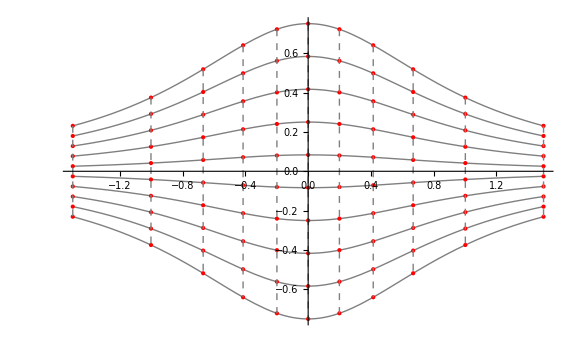

```mathematica
With[{ξ=1,y0=1.5,ny=9,Δ1=1,nq1=5},
Block[{x,q1,y0s,gridpts},
y0s=Range[ny,0,-1]y0/ny-y0/2;
q1=Divide[ArcTan[ξ y0],ξ Δ1]Range[-nq1,nq1]/nq1//N;
gridpts=Thread[{Tan[ξ Δ1 q1]/ξ,Divide[#,1+Tan[ξ Δ1 q1]^2]}]&/@y0s;
Show[
Plot[Divide[y0s,1+ξ^2x^2]//Evaluate,{x,-y0,y0},ImageSize->Large,ImagePadding->10,PlotStyle->Directive[Gray,Thickness[Medium]]],
Graphics[{
{Red,PointSize[Medium],Point/@gridpts},
{Gray,Thickness[Medium],Dashed,Line/@Transpose[gridpts]}
}]
]
]
]
```

We want the center grid spacing along the field line to be proportional to B[x,0], i.e., Δx∝B[x,0].
Integrating Δ_1 ⅆ q^1=ⅆx/(1+ξ^2 x^2), Δ_1 q^1=1/ξ tan^-1 ξ x+ℂ.
To make q^1[x=0]=0, we choose ℂ=0.
The horizontal grid spacing across the field line at the equator is constant.
Then the curvilinear coordinates are
(Δ_1 q^1
Δ_2 q^2)=(1/ξ tan^-1 ξ x
(1+ξ^2 x^2)y), where Δ_1 and Δ_2 are constant scale factors, and q^1 and q^2 are nondimensional.
Inverse of them are
(x
y)=(1/ξ tan[ξ Δ_1 q^1]
(Δ_2 q^2)/(1+tan^2[ξ Δ_1 q^1]))=(1/ξ tan[ξ Δ_1 q^1]
Δ_2 q^2 cos^2[ξ Δ_1 q^1]).
If ξ→0,
(x
y)=(Δ_1 q^1
Δ_2 q^2).

```mathematica
With[{assume=And[q1∈Reals,q2∈Reals,ξ≥0,Δ1>0,Δ2>0,x∈Reals,y∈Reals]},
Module[{g1,g2,gij,g,h1,h2,hij},
g1=D[{Tan[ξ Δ1 q1]/ξ,Δ2 q2 Cos[ξ Δ1 q1]^2},q1];
g1=g1/.{q1->ArcTan[ξ x]/(ξ Δ1),q2->(1+ξ^2x^2)y/Δ2};
g2=D[{Tan[ξ Δ1 q1]/ξ,Δ2 q2 Cos[ξ Δ1 q1]^2},q2];
g2=g2/.{q1->ArcTan[ξ x]/(ξ Δ1),q2->(1+ξ^2x^2)y/Δ2};
gij=FullSimplify[{{g1.g1,g1.g2},{g2.g1,g2.g2}},Assumptions->assume];
(*FullSimplify[gij/.{x->Tan[ξ Δ1 q1]/ξ,y->Δ2 q2 Cos[ξ Δ1 q1]^2},Assumptions->assume]//MatrixForm*)
g=FullSimplify[Det[gij],Assumptions->assume];
h1=FullSimplify[Cross[Append[g2,0],{0,0,1}]/Sqrt[g]//Most,Assumptions->assume];
(*FullSimplify[h1/.{x->Tan[ξ Δ1 q1]/ξ,y->Δ2 q2 Cos[ξ Δ1 q1]^2},Assumptions->assume]*)
h2=FullSimplify[Cross[{0,0,1},Append[g1,0]]/Sqrt[g]//Most,Assumptions->assume];
(*FullSimplify[h2/.{x->Tan[ξ Δ1 q1]/ξ,y->Δ2 q2 Cos[ξ Δ1 q1]^2},Assumptions->assume]*)
hij=FullSimplify[{{h1.h1,h1.h2},{h2.h1,h2.h2}},Assumptions->assume];
(*FullSimplify[hij/.{x->Tan[ξ Δ1 q1]/ξ,y->Δ2 q2 Cos[ξ Δ1 q1]^2},Assumptions->assume]//MatrixForm*)
]
]
```

Covariant bases:
𝕘_1=(∂𝕣)/(∂q^1)=Δ_1(sec^2[ξ Δ_1 q^1]𝕖_x-ξ Δ_2 q^2 sin[2ξ Δ_1 q^1]𝕖_y)=Δ_1((1+ξ^2 x^2)𝕖_x-2 ξ^2 x y 𝕖_y)=Δ_1 𝔹/B_0
𝕘_2=(∂𝕣)/(∂q^2)=Δ_2 cos^2[ξ Δ_1 q^1]𝕖_y=Δ_2/(1+ξ^2 x^2)𝕖_y
Covariant metric tensor:
g_ij=(Δ_1^2(4 ξ^4 x^2 y^2+(1+ξ^2 x^2)^2) | Δ_1 Δ_2(-2 ξ^2 x y)/(1+ξ^2 x^2)
Δ_1 Δ_2(-2 ξ^2 x y)/(1+ξ^2 x^2) | Δ_2^2/((1+ξ^2 x^2)^2))=(Δ_1^2(sec^4[ξ Δ_1 q^1]+(ξ Δ_2 q^2)^2 sin^2[2ξ Δ_1 q^1]) | Δ_1 Δ_2(-ξ Δ_2 q^2 sin[2ξ Δ_1 q^1]cos^2[ξ Δ_1 q^1])
Δ_1 Δ_2(-ξ Δ_2 q^2 sin[2ξ Δ_1 q^1]cos^2[ξ Δ_1 q^1]) | Δ_2^2 cos^4[ξ Δ_1 q^1])
Determinant:
g=Det[g_ij]=(Δ_1 Δ_2)^2
Contravariant bases:
𝕘^1=(𝕘_2×𝕘_3)/(√g)=1/Δ_1 1/(1+ξ^2 x^2)𝕖_x=(cos^2[ξ Δ_1 q^1])/Δ_1 𝕖_x
𝕘^2=(𝕘_3×𝕘_1)/(√g)=1/Δ_2(2 ξ^2 x y 𝕖_x+(1+ξ^2 x^2)𝕖_y)=1/Δ_2(ξ Δ_2 q^2 sin[2ξ Δ_1 q^1]𝕖_x+sec^2[ξ Δ_1 q^1]𝕖_y)
Contravariant metric tensor:
g^ij=(1/Δ_1^2 1/((1+ξ^2 x^2)^2) | 1/(Δ_1 Δ_2)(2 ξ^2 x y)/(1+ξ^2 x^2)
1/(Δ_1 Δ_2)(2 ξ^2 x y)/(1+ξ^2 x^2) | 1/Δ_2^2(4 ξ^4 x^2 y^2+(1+ξ^2 x^2)^2))=(1/Δ_1^2 cos^4[ξ Δ_1 q^1] | 1/(Δ_1 Δ_2)(ξ Δ_2 q^2 sin[2ξ Δ_1 q^1]cos^2[ξ Δ_1 q^1])
1/(Δ_1 Δ_2)(ξ Δ_2 q^2 sin[2ξ Δ_1 q^1]cos^2[ξ Δ_1 q^1]) | 1/Δ_2^2(sec^4[ξ Δ_1 q^1]+(ξ Δ_2 q^2)^2 sin^2[2ξ Δ_1 q^1]))
Field-aligned unit vectors:
𝕖_∥=𝕖_1=𝕘_1/(|𝕘_1|)
𝕖_⊥=𝕖^2=𝕘^2/(|𝕘^2|)
𝕖_(⊥⊥)=𝕖_3=𝕖_z

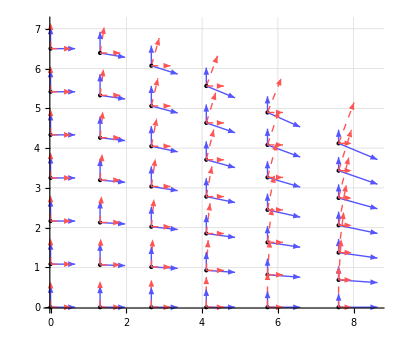

```mathematica
With[{ξ=.1,Δ1=1.3,Δ2=1.0833333333333333,nq1=5,nq2=6},
Module[{Δ1q1,Δ2q2,xy,g1,g2,h1,h2},
Δ1q1=Range[0,nq1]Δ1;
Δ2q2=Range[0,nq2]Δ2;
xy=Thread[{If[Chop[ξ]==0,#,Tan[ξ#]/ξ],Δ2q2 Cos[ξ#]^2}]&/@Δ1q1;
g1=Apply[Function[{x,y},Δ1{1+x^2,-2x y}],ξ xy,{-2}].5;
g2=Apply[Function[{x,y},Δ2{0,1/(1+x^2)}],ξ xy,{-2}].5;
h1=Apply[Function[{x,y},{1/(1+x^2),0}/Δ1],ξ xy,{-2}].5Δ1 Δ2;
h2=Apply[Function[{x,y},{2x y,1+x^2}/Δ2],ξ xy,{-2}].5Δ1 Δ2;
Graphics[{
{Black,PointSize[Medium],Point/@xy},
{Lighter@Blue(*,Thickness[Medium]*),Arrowheads[Small],MapThread[Translate[Arrow[{{0,0},#}],#2]&,Join@@@{g1,xy}],MapThread[Translate[Arrow[{{0,0},#}],#2]&,Join@@@{g2,xy}]},
{Lighter@Red,Thickness[Medium],Dashed,Arrowheads[Small],MapThread[Translate[Arrow[{{0,0},#}],#2]&,Join@@@{h2,xy}],MapThread[Translate[Arrow[{{0,0},#}],#2]&,Join@@@{h1,xy}]}
},
Axes->True,
AxesOrigin->{-1,-1}.02,
AspectRatio->xy[[1,-1,2]]/xy[[-1,1,1]],
GridLines->Automatic,
GridLinesStyle->LightBlue
]
]
]
```

Vector component transformation
𝕦=u^i 𝕘_i=u_i 𝕘^i=u_x 𝕖_x+u_y 𝕖_y
Contravariant to covariant components:
u_i=𝕦·𝕘_i=g_ij u^j
Contravariant to cartesian components:
(u_x
u_y)=(𝕦·𝕖_x
𝕦·𝕖_y)=(u^1 𝕘_1·𝕖_x+u^2 𝕘_2·𝕖_x
u^1 𝕘_1·𝕖_y+u^2 𝕘_2·𝕖_y)
Cartesian to contravariant components:
u^i=𝕦·𝕘^i=u_x 𝕖_x·𝕘^i+u_y 𝕖_y·𝕘^i

```mathematica
With[{ξ=.1,Δ1=1.3,Δ2=1.0833333333333333,x=4,y=3,cartsU={1,3}},
Module[{q1,q2,g1,g2,h1,h2,gij,contrU,covarU,hij},
q1=If[Chop[ξ]==0,x,ArcTan[ξ x]/ξ ]/Δ1;
q2=(1+ξ^2x^2)y/Δ2;
g1=Δ1{1+ξ^2x^2,-2ξ^2x y};
g2=Δ2{0,1/(1+ξ^2x^2)};
h1={1/(1+ξ^2x^2),0}/Δ1;
h2={2ξ^2x y,1+ξ^2x^2}/Δ2;
gij={{g1.g1,g1.g2},{g2.g1,g2.g2}};
hij={{h1.h1,h1.h2},{h2.h1,h2.h2}};
contrU=Plus@@@{cartsU h1,cartsU h2};
covarU=gij.contrU;
{contrU,hij.covarU};
NumberForm[hij,15]
]
]
```

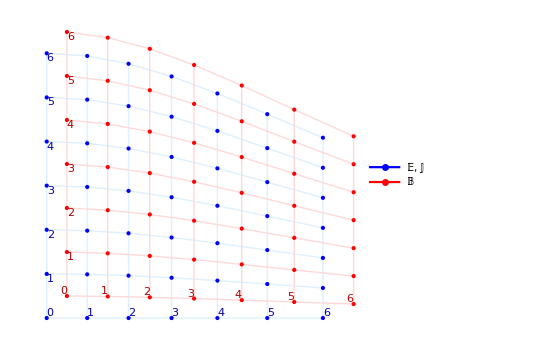

```mathematica
With[{ξ=.1,Δ1=1,Δ2=1,nq1=6,nq2=6},
If[ξ Δ1 nq1≥π/2,Abort[]];
Module[{Δ1q1,Δ2q2,xyF,xyH},
Δ1q1=Range[0,nq1]Δ1;
Δ2q2=Range[0,nq2]Δ2;
xyF=Thread[{If[Chop[ξ]==0,#,Tan[ξ#]/ξ],Δ2q2 Cos[ξ#]^2}]&/@Δ1q1;
xyH=Thread[{If[Chop[ξ]==0,#,Tan[ξ#]/ξ],(Δ2q2+.5Δ2)Cos[ξ#]^2}]&/@(Δ1q1+.5Δ1);
Legended[
Graphics[{
{LightBlue,Thickness[Medium],Line/@xyF,Line/@Thread[xyF]},
{LightRed,Thickness[Medium],Line/@xyH,Line/@Thread[xyH]},
{Blue,PointSize[Medium],Point/@xyF},
{Red,PointSize[Medium],Point/@xyH},
{Darker@Blue,MapIndexed[Text[First[#2]-1,#,{-1,-1}]&,First/@xyF],Rest@MapIndexed[Text[First[#2]-1,#,{-1,1}]&,First@xyF]},
{Darker@Red,MapIndexed[Text[First[#2]-1,#,{1,-1}]&,First/@xyH],Rest@MapIndexed[Text[First[#2]-1,#,{-1,1}]&,First@xyH]}
},
AspectRatio->xyF[[1,-1,2]]/xyF[[-1,1,1]],
Axes->False,
Ticks->False,
BaseStyle->11
],
Placed[PointLegend[{Blue,Red},{"𝔼, 𝕁","𝔹"},Joined->True,LegendMarkers->"●",LegendMarkerSize->Large,LegendLayout->"Row"],Above]
]
]
]
```